# Simple NDSolve Example

## by Prof. Lee Bardwell, Univ. of Calif., Irvine version 11 January 2018

## See my notebook “Binding&NDSolve” for more detailed explanations of what InterpolatingFunctions are, etc.

```mathematica
ClearAll["Global`*"]

(* defining system and giving numerical values to parameters *)
system1 = {
Y'[t] == -k Y[t], Y[0]==Yzero
};
parameters1 = {k->1,Yzero-> 10};
case1 = system1/.parameters1;

(* getting the numerical solution *)solution1 = NDSolve[case1,Y[t],{t,0,20}]
```

{{Y[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

```mathematica
(* getting the value of Y at at particular time, in this case, t = 2 *)
Y[t]/.solution1/.t-> 2.0
```

{1.35335}

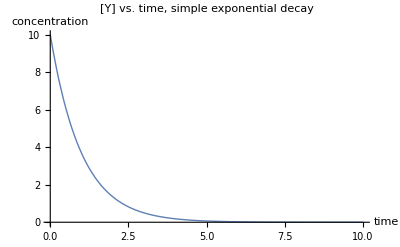

```mathematica
(* plotting the solution *)
Plot[{Y[t]/.solution1},{t,0,10},PlotStyle->Thick,PlotRange->{0,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"]
```

Manipulating plots of NDSolved solutions

```mathematica
(* Manipulating the solution *)
(* Using this method we can leave the system outside of Manipulate, but we need to use "dummy variables" (such as kValue, below) for the parameters we want to manipulate *)

Manipulate[
parameters2= {k->kValue,Yzero-> 10};
solution2 = NDSolve[system1/.parameters2,Y[t],{t,0,20}];
Plot[{Y[t]/.solution2},{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"],
{kValue,0.2,10}
]
```

```mathematica
(* Alternative method for Manipulate using Evaluate *)
(* For this method, the system needs to be defined inside Manipulate, but we don't need to use dummy variables *)

Manipulate[
system2= {Y'[t] == -k Y[t], Y[0]==Yzero};
Plot[Evaluate[Y[t]/.NDSolve[system2,Y[t],{t,0,20}]],{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, simple exponential decay"],
{k,0.2,10},
{Yzero,10,0}
]
```

```mathematica
(* Manipulating the plot of more than 1 state variable *)

Manipulate[
system3= {Y'[t] == -k Y[t], Z[t]== Yzero-Y[t],Y[0]==Yzero};
Plot[Evaluate[{Y[t],Z[t]}/.NDSolve[system3,{Y[t],Z[t]},{t,0,20}]],{t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] and [Z] vs. time,"],
{k,0.2,10},
{Yzero,10,0}
]
```

```mathematica
(* By using "With" we can leave the system outside of Manipulate, while still avoiding the use of dummy variables *)

system4= {Y'[t] == -k Y[t], Z[t]== Yzero-Y[t],Y[0]==Yzero};
With[{f=system4}, Manipulate[Plot[Evaluate[{Y[t],Z[t]}/.NDSolve[f,{Y[t],Z[t]},{t,0,20}]], {t,0,20},PlotStyle->Thick,PlotRange->{-0.2,10},AxesLabel->{"time","concentration"},PlotLabel->"[Y] and [Z] vs. time,"],
{k,0.2,10},
{Yzero,10,0}]]
```

```mathematica
(* Optional way to call NDSolve, using Flatten to remove a set of parenthesis *)solution2= Flatten[NDSolve[case1,Y[t],{t,0,20}]]
```

{Y[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}

```mathematica
(* Note the values are no longer wrapped in parenthesis *)
Y[t]/.solution2/.t-> 2.0
```

1.35335